# HW 3 - ASTR404

## Daniel George - dgeorge5@illinois.edu

## Q5)

## a)

### Mean free path

The mean free path λ is given by:

λ==1/(κ ρ)

Substituting values at the center of the sun:

```mathematica
λ->1/(.217 Quantity[, ("Meters")^2/("Kilograms")]1.53 10^5 Quantity[, ("Kilograms")/("Meters")^3])
```

λ→0.0000301196 m

## b)

### Using a Monte Carlo random walk simulation

#### Distance traveled in time T averaged over 500 runs

```mathematica
d[T_]:=With[{λ=0.0000301195747116,s=500,c=299792458 },ParallelSum[Norm@Total[λ RandomPoint[Sphere[],T c/λ//Floor]],s]/s]
```

#### Computing distances traveled in different times

```mathematica
data={#,d@#}&/@(10.^Range[-11,-7,.1]);
```

#### Plotting distance vs time and the best fit line

Meters traveled in T seconds is approximately:

87.6845 T^0.500276

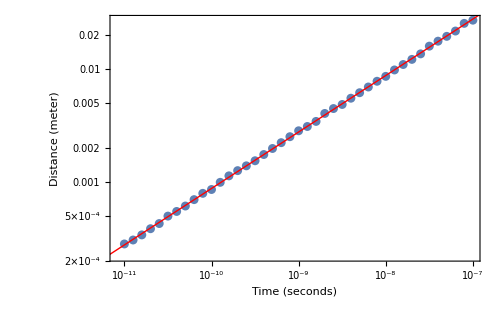

```mathematica
Print["Meters traveled in T seconds is approximately: "];fit=E^LinearModelFit[Log@data,{x},x][Log@T]//Echo;Show[ListLogLogPlot[data,Frame->True,PlotRange->All,ImageSize->500,FrameLabel->{"Time (seconds)","Distance (meter)"}],LogLogPlot[Evaluate@fit,{T,10^-13,10^-5},PlotStyle->{Thin,Red}]]
```

#### A good guess for the distance formula

```mathematica
d==FindFormula[data][T]
```

d==87.0578 √T

#### Extrapolating the formula to find time to reach surface

```mathematica
UnitConvert[Solve[QuantityMagnitude["SolarRadius","Meters"]==FindFormula[data][T],T][[1,1,2]]Quantity[, "Seconds"],"Years"]
```

2.02382×10^6 yr

Therefore the average time required to reach the surface is about 2 million years.

### Using analytic formula for random walk in 3D

#### The analytic formula for the mean distance in d-dimensions for a random-walk after N steps is:

mean distance==(√((2 N)/d) (d+1)/2)/(d/2)

#### Plugging in numbers for our problem:

```mathematica
dT=Sqrt[0.0000301195747116 299792458T]Gamma[2]/Gamma[3/2] Sqrt[2/3]
```

87.5476 √T

#### Computing time taken to reach surface

```mathematica
UnitConvert[Solve[QuantityMagnitude["SolarRadius","Meters"]==dT,T][[1,1,2]]Quantity[, "Seconds"],"Years"]
```

2.00124×10^6 yr

This matches well with our previous numerical estimate.

## Q4)

### Importing data from file

```mathematica
SetDirectory["C:\\Users\\dan7g\\Google Drive\\Acads\\ASTR404\\"];
dataS=SemanticImport["eker_2014_simple.dat"];
```

### Calculating surface gravity and plotting

```mathematica
Show[ListLogLogPlot[dataS[All,#],PlotStyle:>RandomChoice[{Red,Blue}],ImageSize->550,PlotMarkers->"*",Frame->True,FrameLabel->{"Mass in solar units","Gravity at surface in solar units"},PlotRange->All]&/@{<|"M1"->#M1,"g1"->#M1/#R1^2|>&,<|"M2"->#M2,"g2"->#M2/#R2^2|>&}]
```

-Graphics-

There is a large variance in the surface gravity vs mass. However, it can be seen that higher mass stars generally have a lower surface gravity.

## Q3)

### Equations

Let M be the total mass of the system, then we have the following equations:

```mathematica
eqs=
{MHI+MHII-> X*M,
MHeI+MHeII+MHeIII-> Y*M,
MHII->xHII(MHI+MHII),
MHeII->xHeII(MHeI+MHeII+MHeIII),
MHeIII-> xHeIII(MHeI+MHeII+MHeIII),
Me->MHII me/mp+MHeII me/(4mp)+2 MHeIII me/(4mp)};
```

### Mean mass in atomic units

The inverse of the mean mass is given as:

1/μ==m_p/M ∑_(i=1)^n (M(i))/(m(i))

Where m(i) is the mass of a particle, and M(i) is the total mass, of the i’th species. In this case we have:

```mathematica
eqμ=1/μ==mp/M((MHI+MHII)/mp+(MHeI+MHeII+MHeIII)/(4mp)+Me/me)
```

1/μ==((Me/me+(MHeI+MHeII+MHeIII)/(4 mp)+(MHI+MHII)/mp) mp)/M

### Solving for μ

Substituting the first set of equations in the above equation and simplifying, we get:

```mathematica
1/μ==FullSimplify[eqμ[[2]]//.eqs]
```

1/μ==X (1+xHII)+1/4 (1+xHeII+2 xHeIII) Y

QED.

## Q2)

### Substituting values in Saha equation

```mathematica
eqSaha//.{Z2->1,Z1->2,χ->qM[13.6 Quantity[, "Electronvolts"],"SI"],ne->6.1 10^31,T->15.7 10^6}/.consts
```

NII/NI==2.43789

For such high temperatures Z1 cannot be taken as 2 since other terms in the series will become significant.

### Computing correct value of the Z1 for 20 excited states

```mathematica
NSum[2n^2 Exp[qM[-13.6 Quantity[, "Electronvolts"],"SI"](1-1/n^2)/(k 1.5 10^6)]/.consts,{n,20}]
```

5170.56

It can be seen that Z1 diverges to infinity for temperatures this high. Also the assumption that electrons do not interact with neighboring nuclei will break down at these temperatures. Therefore the Boltzmann and Saha equations are probably not valid in this regime.

## Q1)

#### Defining constants in SI units

```mathematica
qM=QuantityMagnitude;
consts={h->qM[Quantity[, "PlanckConstant"],"J s"],me->qM[Quantity[, "ElectronMass"],"kg"],mp->qM[Quantity[, "ProtonMass"],"kg"],k->qM[Quantity[, "BoltzmannConstant"],"J/K"]};
```

## a)

### Defining the Saha equation for singly ionized H

```mathematica
eqSaha=NII /NI==2/ne /Sqrt[h^2/(2 Pi me k T)]^3 (Z2/Z1)Exp[-χ/(k T)]
```

NII/NI==(4 √2 ⅇ^(-χ/(k T)) π^(3/2) Z2)/(ne (h^2/(k me T))^(3/2) Z1)

### Substituting values for constants

Assuming Z2 = 1, Z1 ~ 2, χ = 13.6 eV, n_e = NII / V, and V = (NI+NII) m_p / ρ and x = NII / (NI+NII)

```mathematica
eqS=eqSaha//.{Z2->1,Z1->2,χ->qM[13.6 Quantity[, "Electronvolts"],"SI"],V-> (NI+NII)mp /ρ,ne->NII/V,ρ->10^-6.}/.consts;
```

### Rewriting the above equation in terms of ionization fraction x

```mathematica
eqx=x(1-x)#&/@eqS/.NII->x NI/(1-x)//Simplify
```

x^2==1/(1/T)^(3/2)ⅇ^(-157822./T) (4.03885-4.03885 x)

This is a quadratic equation for the ionization fraction (x).

## b)

### Plotting ionization fraction vs temperature

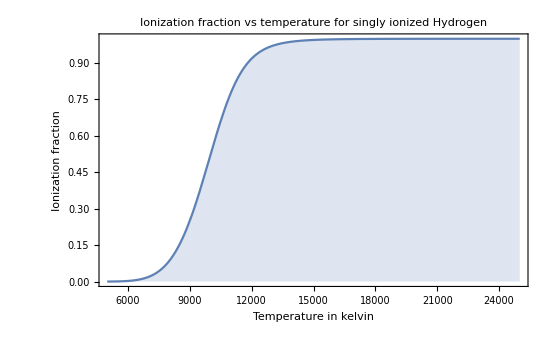

```mathematica
Plot[Quiet@Solve[eqx&&x>0,x][[1,1,2]],{T,5000,25000},Frame->True,Filling->Bottom,ImageSize->550,FrameLabel->{"Temperature in kelvin","Ionization fraction"},PlotLabel->"Ionization fraction vs temperature for singly ionized Hydrogen"]
```